```mathematica
rise=Import["C:\\Users\\Dani\\Desktop\\control\\rise_agua.csv","Table","FieldSeparators"->";"];
```

```mathematica
nlm=NonlinearModelFit[rise,a*(Exp[-b*t]),{{a,1},{b,0}},t];
```

```mathematica
nlm["AdjustedRSquared"]
```

0.997295

```mathematica
agua[t_]=nlm["BestFit"]
```

22.2857 ⅇ^(0.00183891 t)

```mathematica
agua[s_]=LaplaceTransform[agua[t],t,s]
```

22.2857/(-0.00183891+s)

```mathematica
fit[t_]=-121.1*ⅇ^(-0.002049*t)+117.8*ⅇ^(-8.03*(10^-5)*t)
```

-121.1 ⅇ^(-0.002049 t)+117.8 ⅇ^(-0.0000803 t)

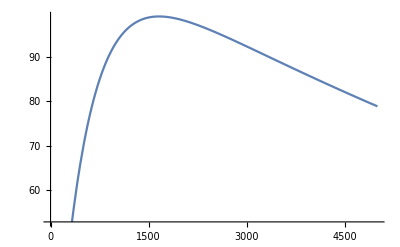

```mathematica
Plot[-121.1 ⅇ^(-0.002049 t)+117.8 ⅇ^(-0.0000803 t),{t,0,5000}]
```